# Coupled oscillators between fixed walls

The system consists of two equal unit masses (m=1) attached together by three springs with spring-constants, respectively: 1, K and 1. 
There is therefore a ‘coupling’  force c between the two masses, which would otherwise oscillate independently.

This is the general solution with four integration constants and a sum of two normal modes. It appears a little difficult to interpret because the result is given after complexification.

```mathematica
DSolve[{x''[t]+ (1+K)x[t]-K y[t]==0,y''[t]+(1+K) y[t]-K x[t]==0},{x[t],y[t]},t]
```

{{x[t]→1/4 ⅇ^(-ⅈ t-√(-1-2 K) t) (ⅇ^(ⅈ t)+ⅇ^(√(-1-2 K) t)+ⅇ^(2 ⅈ t+√(-1-2 K) t)+ⅇ^(ⅈ t+2 √(-1-2 K) t)) C[1]+(ⅇ^(-ⅈ t-√(-1-2 K) t) (-ⅇ^(ⅈ t)+ⅇ^(ⅈ t+2 √(-1-2 K) t)+ⅈ ⅇ^(√(-1-2 K) t) √(-1-2 K)-ⅈ ⅇ^(2 ⅈ t+√(-1-2 K) t) √(-1-2 K)) C[2])/(4 √(-1-2 K))+1/4 ⅇ^(-ⅈ t-√(-1-2 K) t) (-ⅇ^(ⅈ t)+ⅇ^(√(-1-2 K) t)+ⅇ^(2 ⅈ t+√(-1-2 K) t)-ⅇ^(ⅈ t+2 √(-1-2 K) t)) C[3]+(ⅇ^(-ⅈ t-√(-1-2 K) t) (ⅇ^(ⅈ t)-ⅇ^(ⅈ t+2 √(-1-2 K) t)+ⅈ ⅇ^(√(-1-2 K) t) √(-1-2 K)-ⅈ ⅇ^(2 ⅈ t+√(-1-2 K) t) √(-1-2 K)) C[4])/(4 √(-1-2 K)),y[t]→1/4 ⅇ^(-ⅈ t-√(-1-2 K) t) (-ⅇ^(ⅈ t)+ⅇ^(√(-1-2 K) t)+ⅇ^(2 ⅈ t+√(-1-2 K) t)-ⅇ^(ⅈ t+2 √(-1-2 K) t)) C[1]+(ⅇ^(-ⅈ t-√(-1-2 K) t) (ⅇ^(ⅈ t)-ⅇ^(ⅈ t+2 √(-1-2 K) t)+ⅈ ⅇ^(√(-1-2 K) t) √(-1-2 K)-ⅈ ⅇ^(2 ⅈ t+√(-1-2 K) t) √(-1-2 K)) C[2])/(4 √(-1-2 K))+1/4 ⅇ^(-ⅈ t-√(-1-2 K) t) (ⅇ^(ⅈ t)+ⅇ^(√(-1-2 K) t)+ⅇ^(2 ⅈ t+√(-1-2 K) t)+ⅇ^(ⅈ t+2 √(-1-2 K) t)) C[3]+(ⅇ^(-ⅈ t-√(-1-2 K) t) (-ⅇ^(ⅈ t)+ⅇ^(ⅈ t+2 √(-1-2 K) t)+ⅈ ⅇ^(√(-1-2 K) t) √(-1-2 K)-ⅈ ⅇ^(2 ⅈ t+√(-1-2 K) t) √(-1-2 K)) C[4])/(4 √(-1-2 K))}}

We can identify a normal mode by introducing initial conditions in which both x and y move by the same amount. This normal mode has omega=1.
We use the “Flatten” command to remove one of the parentheses:

```mathematica
sol1=Flatten[DSolve[{x''[t]+ (1+K)x[t]-K y[t]==0,y''[t]+(1+K) y[t]-K x[t]==0,x[0]==1,x'[0]==0,y[0]==1,y'[0]==0},{x[t],y[t]},t]]
```

{x[t]→1/2 ⅇ^(-ⅈ t) (1+ⅇ^(2 ⅈ t)),y[t]→1/2 ⅇ^(-ⅈ t) (1+ⅇ^(2 ⅈ t))}

Let’s extract the real part of the solution:

```mathematica
x[t]/.sol1//Rationalize[#,0]&//Re//ComplexExpand[#,TargetFunctions->{Re,Im}]&//FullSimplify
y[t]/.sol1//Rationalize[#,0]&//Re//ComplexExpand[#,TargetFunctions->{Re,Im}]&//FullSimplify
```

Cos[t]

Cos[t]

Another, step by step method to get the same result is done as follows: 
First choose the x[t] part of the solution

```mathematica
x[t]/.sol1
```

1/2 ⅇ^(-ⅈ t) (1+ⅇ^(2 ⅈ t))

Expand to multiply out

```mathematica
Expand[x[t]/.sol1]
```

ⅇ^(-ⅈ t)/2+ⅇ^(ⅈ t)/2

Finally, ComplexExpand provides the answer in simple form, which is real because the initial conditions are real.

```mathematica
ComplexExpand[Expand[x[t]/.sol1]]
```

Cos[t]

```mathematica
ComplexExpand[Expand[y[t]/.sol1]]
```

Cos[t]

Here's the other normal mode, where x=-y, and omega=Sqrt[1+2c] (when K=1):

```mathematica
sol2=Flatten[DSolve[{x''[t]+ (1+K)x[t]-K y[t]==0,y''[t]+(1+K) y[t]-K x[t]==0,x[0]==1,x'[0]==0,y[0]==-1,y'[0]==0},{x[t],y[t]},t]]
```

{x[t]→1/2 ⅇ^(-√(-1-2 K) t) (1+ⅇ^(2 √(-1-2 K) t)),y[t]→-1/2 ⅇ^(-√(-1-2 K) t) (1+ⅇ^(2 √(-1-2 K) t))}

```mathematica
{x[t]->1/2 ⅇ^(-√(-1-2 K) t) (1+ⅇ^(2 √(-1-2 K) t)),y[t]->-1/2 ⅇ^(-√(-1-2 K) t) (1+ⅇ^(2 √(-1-2 K) t))}
```

{x[t]→1/2 ⅇ^(-√(-1-2 K) t) (1+ⅇ^(2 √(-1-2 K) t)),y[t]→-1/2 ⅇ^(-√(-1-2 K) t) (1+ⅇ^(2 √(-1-2 K) t))}

```mathematica
Simplify[ComplexExpand[y[t]/.sol2],K>0]
```

-Cos[√(1+2 K) t]

Here's a solution with boundary conditions that excite both modes:

```mathematica
sol=Flatten[DSolve[{x''[t]+ (1+K)x[t]-K y[t]==0,y''[t]+(1+K) y[t]-K x[t]==0,x[0]==1,x'[0]==0,y[0]==0,y'[0]==0},{x[t],y[t]},t]]
```

{x[t]→1/4 ⅇ^(-ⅈ t-√(-1-2 K) t) (ⅇ^(ⅈ t)+ⅇ^(√(-1-2 K) t)+ⅇ^(2 ⅈ t+√(-1-2 K) t)+ⅇ^(ⅈ t+2 √(-1-2 K) t)),y[t]→-1/4 ⅇ^(-ⅈ t-√(-1-2 K) t) (ⅇ^(ⅈ t)-ⅇ^(√(-1-2 K) t)-ⅇ^(2 ⅈ t+√(-1-2 K) t)+ⅇ^(ⅈ t+2 √(-1-2 K) t))}

Plot for coupling K=1 (the first case discussed in class):

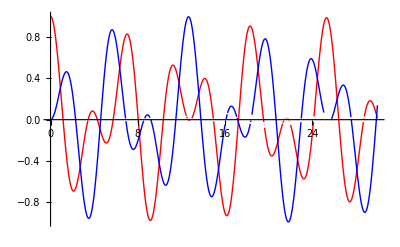

```mathematica
Plot[{x[t]/.sol/.K->1,y[t]/.sol/.K->1},{t,0,30},PlotStyle->{{Thick,Red},{Thick, Blue}}]
```

Weak coupling (K=0.1): notice that x (red) mostly oscillates at first, then y (blue), etc.
This is like the demonstration in class where the energy oscillates back and forward between the two pendula.

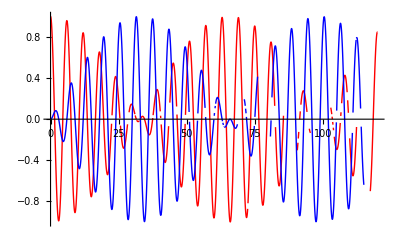

```mathematica
Plot[{x[t]/.sol/.K->.1,y[t]/.sol/.K->.1},{t,0,120},PlotStyle->{{Thick,Red},{Thick, Blue}}]
```

```mathematica
Plot[{x[t]/.sol/.K->.1,y[t]/.sol/.K->.1},{t,0,120},PlotStyle->{{Thick,Red},{Thick, Blue}}]
```

-Graphics-

Very strong coupling (K=5). The two masses oscillate about an envelope corresponding to the low-frequency normal mode.

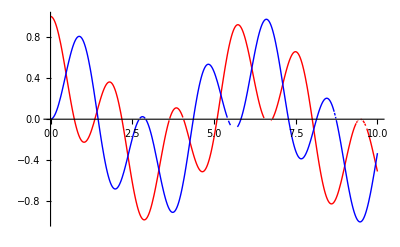

```mathematica
Plot[{x[t]/.sol/.K->5,y[t]/.sol/.K->5},{t,0,10},PlotStyle->{{Thick,Red},{Thick, Blue}}]
```

### Making an animation (essentially equivalent to the coupled pendula demonstration)

Convenient to pull out the functions x[t] and y[t] from solution:

```mathematica
xx[t_]=Re[x[t]]/.sol
```

1/4 Re[ⅇ^(-ⅈ t-√(-1-2 K) t) (ⅇ^(ⅈ t)+ⅇ^(√(-1-2 K) t)+ⅇ^(2 ⅈ t+√(-1-2 K) t)+ⅇ^(ⅈ t+2 √(-1-2 K) t))]

```mathematica
yy[t_]=Re[y[t]]/.sol
```

-1/4 Re[ⅇ^(-ⅈ t-√(-1-2 K) t) (ⅇ^(ⅈ t)-ⅇ^(√(-1-2 K) t)-ⅇ^(2 ⅈ t+√(-1-2 K) t)+ⅇ^(ⅈ t+2 √(-1-2 K) t))]

Place a disc at the positions of the masses, assuming (arbitrarily) that they are 4 apart at rest. K0 is the coupling.

```mathematica
plotosc[t_,K0_]:=Graphics[{Red,Disk[{N[4+xx[t]/.K->K0],0},0.1],Blue,Disk[{N[yy[t]/.K->K0],0},0.1]},Axes->True,PlotRange->{{-1.1,5.1},{-.14,.14}}]
```

Now make a little movie:

With weak coupling (K0 =0.1)

```mathematica
Animate[plotosc[t,0.1],{t,0,100},AnimationRate->1]
```

With strong coupling (K0 = 5)

```mathematica
Animate[plotosc[t,5],{t,0,100},AnimationRate->1]
```

Here’s the first normal mode (which is independent of the coupling K):

```mathematica
xx1[t_]=Re[x[t]]/.sol1 ; yy1[t_]=Re[y[t]]/.sol1;
```

```mathematica
plotosc1[t_]:=Graphics[{Red,Disk[{N[4+xx1[t]],0},0.1],Blue,Disk[{N[yy1[t]],0},0.1]},Axes->True,PlotRange->{{-1.1,5.1},{-.14,.14}}]
```

```mathematica
Animate[plotosc1[t],{t,0,100},AnimationRate->1]
```

Here’s the second normal mode (which idepends on the coupling K, set to 1 below):

```mathematica
xx2[t_]=Re[x[t]]/.sol2; yy2[t_]=Re[y[t]]/.sol2;
```

```mathematica
plotosc2[t_,K0_]:=Graphics[{Red,Disk[{N[4+xx2[t]/.K->K0],0},0.1],Blue,Disk[{N[yy2[t]/.K->K0],0},0.1]},Axes->True,PlotRange->{{-1.1,5.1},{-.14,.14}}]
```

```mathematica
Animate[plotosc2[t,1],{t,0,100},AnimationRate->1]
```